Clear parameters

```mathematica
ClearAll[α,d,ωR,ωE,μ,θA,θB,κ,βRA,βRB,βEA,βEB,τ,PA,PB,RA1,RA2,RA3,RB1,RB2,RB3,EA,EB,i,YA,YB,imax,θanA,RA,RB]
```

Densities

```mathematica
Densities={
EquiRBC=9405500,(*steady state RBC density*)
Atotal=5089828, (*total recipient RBCs in 1 μL*)
Btotal=157417, (*total donor RBCs in 1 μL*)
RAden= Atotal*0.0006, (*total recipient reticulocytes*)
RBden=Btotal*0.0054, (*total donor reticulocytes*)
EAden=Atotal*0.9994, (*total recipient normocytes*)
EBden=Btotal*0.9946, (*total donor normocytes*)
PAden=442593, (*initial recipient parasitaemia*)
PBden=13688} ;(*initial donor parasitaemia*)
```

Parameters

```mathematica
imax=4; μ=0.48; d=0.00025;(*sets parameters*)

βRA=1.45*10^-4;βRB=4.8*10^-4; (*invasion rates*)
βEA=9.67*10^-7;βEB=3.2*^-6; 

ωR=8.12;ωE=7.979;(*Best fit burst sizes for reticulocytes and normocytes*)

θA=0.1; θanA=0.52509; (*recovery coefficient for erythropoesis*)
θB=0;

τ=2; (*lag time for erythropoesis*)

κ=EquiRBC; (*steady state RBC density*)
```

Initial conditions

```mathematica
(*output taken from R Model IV script, outputs 96 and 120 (hours)*)
PA[0] =PAden;
PB[0]=PBden;
RA1[0]=RAden/3;
RB1[0]=RBden/3;
RA2[0] =RAden/3;
RB2[0] =RBden/3;
RA3[0]=RAden/3;
RB3[0]=RBden/3;
EA[0]=EAden;
EB[0]=EBden;
IARA[0]=0;
IBRA[0]=0;
IARB[0]=0;
IBRB[0]=470;
IAEA[0]=0;
IAEB[0]=0;
IBEA[0]=0;
IBEB[0]=13200;
```

Set RBC densities in the past to be equal to densities from R Model IV script, but adjusted to be in 1 μL

```mathematica
(*One day previous*)
RA1[-1]=N[19916771/1462];
RB1[-1]=0.01 71122166/1462;
RA2[-1] =N[13275317/1462];
RB2[-1] =0.01 68274628/1462;
RA3[-1]=N[12534692/1462];
RB3[-1]=0.01 67829481/1462;
EA[-1]=N[7439597666/1462];
EB[-1]=0.01 8525485216/1462;
(*Two days previous*)
RA1[-2]=N[71122166/1462];
RB1[-2]=0.01 86517345/1462;
RA2[-2] =N[68274628/1462];
RB2[-2] =0.01 85907786/1462;
RA3[-2]=N[67829481/1462];
RB3[-2]=0.01 85708581/1462;
EA[-2]=N[8525485216/1462];
EB[-2]=0.01 8760799715/1462;
(*Three days previous*)
RA1[-3]=N[86517345/1462];
RB1[-3]=0.01 90778609/1462;
RA2[-3] =N[85907786/1462];
RB2[-3] =0.01 90447764/1462;
RA3[-3]=N[85708581/1462];
RB3[-3]=0.01 90349959/1462;
EA[-3]=N[8760799715/1462];
EB[-3]=0.01 8820478815/1462;
```

Equations

Denominator for Exp terms

```mathematica
α= (βRA*{RA1[i-1]+RA2[i-1]+RA3[i-1]})+(βRB*{RB1[i-1]+RB2[i-1]+RB3[i-1]})+(βEA*EA[i-1])+(βEB*EB[i-1]);
```

Total reticulocytes from recipient and donor

```mathematica
YA=RA1[i-1]+RA2[i-1]+RA3[i-1];
YB=RB1[i-1]+RB2[i-1]+RB3[i-1];
```

Discrete time equations

```mathematica
For[i =1,i< 4,i++,
If[RA1[i-1]+RA2[i-1]+RA3[i-1]+EA[i-1]<(0.5*EquiRBC),theta=θanA, theta=θA];

PA[i]={(1-d) ωE (EA[-1+i] (1-(ⅇ^(-(βEA (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i]))+EB[-1+i] (1-(ⅇ^(-(βEB (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i])))+ωR (YA (1-(ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i]))+YB (1-(ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i])))};
PB[i]=
{(1-d) ωE (EA[-1+i] (1-(ⅇ^(-(βEA (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i]))+EB[-1+i] (1-(ⅇ^(-(βEB (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i])))+ωR (YA (1-(ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i]))+YB (1-(ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i])))};
RA1[i]=θA (-YA-YB+κ-EA[-1+i]-EB[-1+i]);
RB1[i]=θB (-YA-YB+κ-EA[-1+i]-EB[-1+i]);
RA2[i]=(1-d) ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) RA1[-1+i];
RB2[i]=(1-d) ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) RB1[-1+i];
RA3[i]=(1-d) ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) RA2[-1+i];
RB3[i]=(1-d) ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) RB2[-1+i];
EB[i]=(1-d) (ⅇ^(-(βEB (PA[-1+i]+PB[-1+i]))/α) EB[-1+i]+ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) RB3[-1+i]);
EA[i]=(1-d) (ⅇ^(-(βEA (PA[-1+i]+PB[-1+i]))/α) EA[-1+i]+ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) RA3[-1+i]);
IARA[i]=YA (1-(ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i]));
IARB[i]=YB (1-(ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i]));
IAEA[i]=EA[-1+i] (1-(ⅇ^(-(βEA (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i]));
IAEB[i]=EB[-1+i] (1-(ⅇ^(-(βEB (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i]));
IBRB[i]=YB (1-(ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i]));
IBRA[i]=YA (1-(ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i]));
IBEB[i]=EB[-1+i] (1-(ⅇ^(-(βEB (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i]));
IBEA[i]=EA[-1+i] (1-(ⅇ^(-(βEA (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i]));

];(*end for i loop*)
Aretics=Flatten[Table[RA1[i]+RA2[i]+RA3[i],{i,0,imax-1}]];
Anormos=Flatten[Table[EA[i],{i,0,imax-1}]];
Aa=Aretics+Anormos;
Bretics=Flatten[Table[RB1[i]+RB2[i]+RB3[i],{i,0,imax-1}]];
Bnormos=Flatten[Table[EB[i],{i,0,imax-1}]];
Ba=Bretics+Bnormos;
TotalRBCs=Aa+Ba;

IBAretics=Flatten[Table[IBRA[i],{i,0,imax-1}]];
IBBretics=Flatten[Table[IBRB[i],{i,0,imax-1}]];
IBAnormos=Flatten[Table[IBEA[i],{i,0,imax-1}]];
IBBnormos=Flatten[Table[IBEB[i],{i,0,imax-1}]];
IBB=IBBnormos+IBBretics;
IBA=IBAnormos+IBAretics;
IBtotal=IBB+IBA;
Atab=Flatten[Table[PA[i],{i,0,imax-1}]](*proportion of AS parasites that successfully infect*);
Btab=Flatten[Table[PB[i],{i,0,imax-1}]](*proportion of DK parasites that successfully infect*);
Btotal=Ba+IBB;
```

```mathematica
Atab
```

{442593,4.01233×10^6,4.06043×10^7,1.86377×10^7}

```mathematica
TotalRBCs
```

{5.24725×10^6,5.48477×10^6,3.81549×10^6,2.52345×10^6}

RBCs

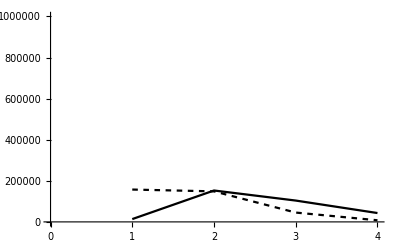

```mathematica
Print["RBCs"]
ListPlot[{IBB,Ba}, Joined->True, PlotRange->{0,10^6},PlotStyle->{Black, Directive[Black, Dashing[0.01]]}] (*Data in dashed line*)
```

```mathematica
PAnext=

ωR*(YA*{1-Exp[-((PA+PB)*βRA)/α]*(PA/(PA+PB))}+YB*{1-Exp[-((PA+PB)*βRB)/α]*(PA/(PA+PB))})+
ωE*(EA*{1-Exp[-((PA+PB)*βEA)/α]*(PA/(PA+PB))}+EB*{1-Exp[-((PA+PB)*βEB)/α]*(PA/(PA+PB))})*(1-d);


PBnext= ωR*(YA*{1-Exp[-((PA+PB)*βRA)/α]*(PB/(PA+PB))}+YB*{1-Exp[-((PA+PB)*βRB)/α]*(PB/(PA+PB))})+
ωE*(EA*{1-Exp[-((PA+PB)*βEA)/α]*(PB/(PA+PB))}+EB*{1-Exp[-((PA+PB)*βEB)/α]*(PB/(PA+PB))})*(1-d);
RA1next=θA*(κ-(YA+YB+EA+EB));
RB1next=θB*(κ-(YA+YB+EA+EB));
RA2next=(RA1*Exp[-((PA+PB)*βRA)/α])*(1-d);
RB2next=(RB1*Exp[-((PA+PB)*βRB)/α])*(1-d);
RA3next=(RA2*Exp[-((PA+PB)*βRA)/α])*(1-d);
RB3next=(RB2*Exp[-((PA+PB)*βRB)/α])*(1-d);
EAnext=(RA3*Exp[-((PA+PB)*βRA)/α]+EA*Exp[-((PA+PB)*βEA)/α])*(1-d);
EBnext=(RB3*Exp[-((PA+PB)*βRB)/α]+EB*Exp[-((PA+PB)*βEB)/α])*(1-d);
```

Parameter substitutions

```mathematica
subIterate = {
PA-> PA[i-1],
PB-> PB[i-1],
RA1-> RA1[i-1],
 RB1->RB1[i-1],
RA2->RA2[i-1],
RB2->RB2[i-1],
RA3->RA3[i-1],
RB3-> RB3[i-1],
EA->EA[i-1],
EB->EB[i-1]

};
```

```mathematica
PAnext/.subIterate
PBnext/.subIterate
RA1next/.subIterate
RB1next/.subIterate
RA2next/.subIterate
RB2next/.subIterate
RA3next/.subIterate
RB3next/.subIterate
EBnext/.subIterate
EAnext/.subIterate
```

{(1-d) ωE (EA[-1+i] (1-(ⅇ^(-(βEA (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i]))+EB[-1+i] (1-(ⅇ^(-(βEB (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i])))+ωR (YA (1-(ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i]))+YB (1-(ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) PA[-1+i])/(PA[-1+i]+PB[-1+i])))}

{(1-d) ωE (EA[-1+i] (1-(ⅇ^(-(βEA (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i]))+EB[-1+i] (1-(ⅇ^(-(βEB (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i])))+ωR (YA (1-(ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i]))+YB (1-(ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) PB[-1+i])/(PA[-1+i]+PB[-1+i])))}

θA (-YA-YB+κ-EA[-1+i]-EB[-1+i])

θB (-YA-YB+κ-EA[-1+i]-EB[-1+i])

(1-d) ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) RA1[-1+i]

(1-d) ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) RB1[-1+i]

(1-d) ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) RA2[-1+i]

(1-d) ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) RB2[-1+i]

(1-d) (ⅇ^(-(βEB (PA[-1+i]+PB[-1+i]))/α) EB[-1+i]+ⅇ^(-(βRB (PA[-1+i]+PB[-1+i]))/α) RB3[-1+i])

(1-d) (ⅇ^(-(βEA (PA[-1+i]+PB[-1+i]))/α) EA[-1+i]+ⅇ^(-(βRA (PA[-1+i]+PB[-1+i]))/α) RA3[-1+i])

Final equations

```mathematica
PA[i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_] :=PA[i,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]= 
{{(1-d) (ωE ((1-ⅇ^(-(βEA PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+(1-ⅇ^(-(βEB PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+ωR ((1-ⅇ^(-(βRA PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+(1-ⅇ^(-(βRB PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))}};
PB[i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_] :=PB[i,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]=
{{(1-d) (ωE ((1-ⅇ^(-(βEA PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+(1-ⅇ^(-(βEB PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+ωR ((1-ⅇ^(-(βRA PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+(1-ⅇ^(-(βRB PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))}};
RA1[i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_]:=RA1[i,,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]=
θA (κ-EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]);
RB1[ i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_]:=RB1[i,,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]=
θB (κ-EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]-RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]);
RA2[i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_]:=RA2[i,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]=
{{(1-d) (ⅇ^(-(βRA PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))+ⅇ^(-(βRA PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]}};
RB2[i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_]:=RB2[i,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]=
{{(1-d) (ⅇ^(-(βRB PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))+ⅇ^(-(βRB PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]}};
RA3[i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_]:=RA3[i,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]=
{{(1-d) (ⅇ^(-(βRA PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))+ⅇ^(-(βRA PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]}};
RB3[i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_]:=RB3[i,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]=
{{(1-d) (ⅇ^(-(βRB PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))+ⅇ^(-(βRB PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]}};
EB[i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_]:=EB[i,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]=
{{(1-d) ((ⅇ^(-(βEB PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))+ⅇ^(-(βEB PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+(ⅇ^(-(βRB PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))+ⅇ^(-(βRB PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])}};
EA[i_,ωR_, ωE_,βRA_,βRB_,βEA_,βEB_,μ_,d_,θA_,θB_,κ_,τ_]:=EA[i,ωR, ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]=
{{(1-d) ((ⅇ^(-(βEA PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))+ⅇ^(-(βEA PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+(ⅇ^(-(βRA PA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))+ⅇ^(-(βRA PB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])/(μ+βEA EA[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βEB EB[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+βRA (RA1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])+βRB (RB1[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB2[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ]+RB3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])))) RA3[-1+i,ωR,ωE,βRA,βRB,βEA,βEB,μ,d,θA,θB,κ,τ])}};
```

## Code execution

```mathematica
Block[{$RecursionLimit=Infinity},Table[RB3[i,5,5,0.00001,0.00002,0.000001,0.000002,50,0.2,0.1,0,EquiRBC,1],{i,0,3}]]
```

{283.351,{{418.797}},{{{{651.533}}}},{{{{{{0.}}}}}}}